# RRTV Cone Projection

## Conformal Block Definition

```mathematica
k[b_,z_]:=z^(b/2)Hypergeometric2F1[b/2,b/2,b,z];
G[l_,Δ_,z_,zbar_]:= (-1)^l/2^l(z zbar)1/(z-zbar)(-k[Δ-l-2,z]k[Δ+l,zbar]+k[Δ-l-2,zbar]k[Δ+l,z])
```

## Evaluation of F[z,zbar]

### Invariant Cross Ratios Definition

```mathematica
u[z_, zbar_]:= z zbar;
v[z_, zbar_]:=(1-z)(1-zbar)
```

```mathematica
F[d_,l_,Δ_,z_,zbar_]:=(v[z,zbar]^d G[l,Δ,z,zbar]-u[z,zbar]^d G[l,Δ,(1-z),(1-zbar)])/(u[z,zbar]^d-v[z,zbar]^d)
```

```mathematica
Solve[z==1/2+a+b &&zbar==1/2+a-b,{a,b}]//Simplify
```

{{a→1/2 (-1+z+zbar),b→(z-zbar)/2}}

```mathematica
Fab=(v[1/2+a+b,1/2+a-b]^d G[l,Δ,1/2+a+b,1/2+a-b]-u[1/2+a+b,1/2+a-b]^d G[l,Δ,(1-(1/2+a+b)),(1-(1/2+a-b))])/(u[1/2+a+b,1/2+a-b]^d-v[1/2+a+b,1/2+a-b]^d);
```

l = 0

```mathematica
δ2F={δ2aF,δ2bF}={D[Fab,{a,2}],D[Fab,{b,2}]};
```

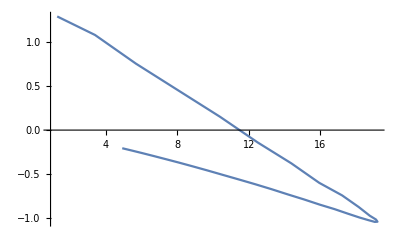

```mathematica
{lVal,dVal}={2,1};
δ2FTable2=Table[{ΔVal,δ2aF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal},δ2bF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal}},{ΔVal,4,20,0.5}];
p2={δ2aF/.{a->0.0001,b->0.0001,l->2,Δ->4,d->1},δ2bF/.{a->0.0001,b->0.0001,l->2,Δ->4,d->1}};
ListPlot[Transpose[{δ2FTable2[[All,2]],δ2FTable2[[All,3]]}],PlotRange->All,Joined->True]
```

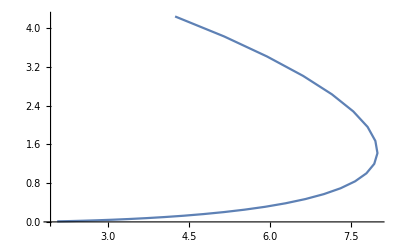

```mathematica
{lVal,dVal}={4,1};
δ2FTable4=Table[{ΔVal,δ2aF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal},δ2bF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal}},{ΔVal,6,20,0.5}];
ListPlot[Transpose[{δ2FTable4[[All,2]],δ2FTable4[[All,3]]}],PlotRange->All,Joined->True]
```

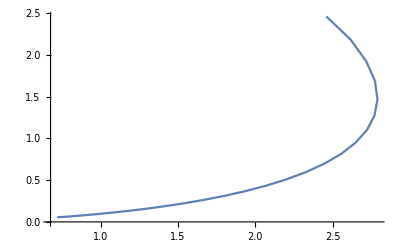

```mathematica
{lVal,dVal}={6,1};
δ2FTable6=Table[{ΔVal,δ2aF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal},δ2bF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal}},{ΔVal,8,20,0.5}];
ListPlot[Transpose[{δ2FTable6[[All,2]],δ2FTable6[[All,3]]}],PlotRange->All,Joined->True]
```

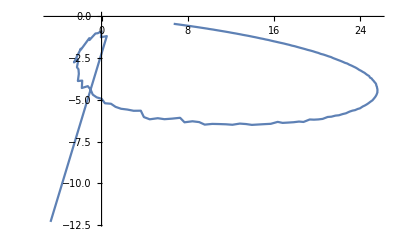

```mathematica
{lVal,dVal}={0,1};
δ2FTable0=Table[{ΔVal,δ2aF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal},δ2bF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal}},{ΔVal,1.01,20,0.1}];
ListPlot[Transpose[{δ2FTable0[[All,2]],δ2FTable0[[All,3]]}],PlotRange->All,Joined->True]
```

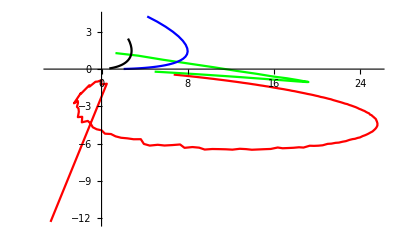

```mathematica
Show[ListPlot[Transpose[{δ2FTable0[[All,2]],δ2FTable0[[All,3]]}],PlotRange->All,Joined->True,PlotStyle->Red],
ListPlot[Transpose[{δ2FTable2[[All,2]],δ2FTable2[[All,3]]}],PlotRange->All,Joined->True,PlotStyle->Green],
ListPlot[Transpose[{δ2FTable4[[All,2]],δ2FTable4[[All,3]]}],PlotRange->All,Joined->True,PlotStyle->Blue],
ListPlot[Transpose[{δ2FTable6[[All,2]],δ2FTable6[[All,3]]}],PlotRange->All,Joined->True,PlotStyle->Black],PlotRange->All]
```

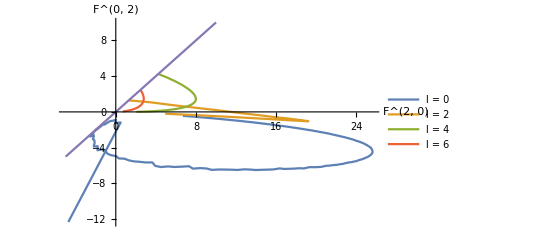

```mathematica
ListPlot[{Transpose[{δ2FTable0[[All,2]],δ2FTable0[[All,3]]}],
Transpose[{δ2FTable2[[All,2]],δ2FTable2[[All,3]]}],
Transpose[{δ2FTable4[[All,2]],δ2FTable4[[All,3]]}],
Transpose[{δ2FTable6[[All,2]],δ2FTable6[[All,3]]}],
Transpose[{Table[x,{x,-5,10}],Table[p2[[2]]/p2[[1]] x,{x,-5,10}]}]},PlotRange->All,Joined->True,PlotLegends->{"l = 0","l = 2","l = 4","l = 6"},AxesLabel->{"F^(2, 0)","F^(0, 2)"}]
```

```mathematica
projectd1=ListPlot[{Transpose[{δ2FTable0[[All,2]],δ2FTable0[[All,3]]}],
Transpose[{δ2FTable2[[All,2]],δ2FTable2[[All,3]]}],
Transpose[{δ2FTable4[[All,2]],δ2FTable4[[All,3]]}],
Transpose[{δ2FTable6[[All,2]],δ2FTable6[[All,3]]}],
Transpose[{Table[x,{x,-5,10}],Table[p2[[2]]/p2[[1]] x,{x,-5,10}]}]},PlotRange->All,Joined->True,PlotLegends->{"l = 0","l = 2","l = 4","l = 6"},AxesLabel->{"F^(2, 0)","F^(0, 2)"}]
Export["projectd1.jpg",projectd1]
```

-Graphics-

projectd1.jpg

## d>1 but near 1... So far we analysed for d=1... Now set d=1.05

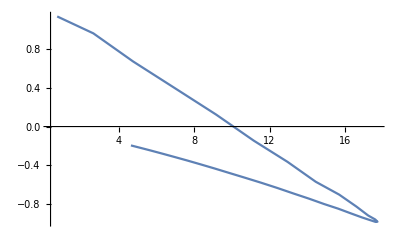

```mathematica
{lVal,dVal}={2,1.05};
δ2FTable2=Table[{ΔVal,δ2aF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal},δ2bF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal}},{ΔVal,4,20,0.5}];
ListPlot[Transpose[{δ2FTable2[[All,2]],δ2FTable2[[All,3]]}],PlotRange->All,Joined->True]
```

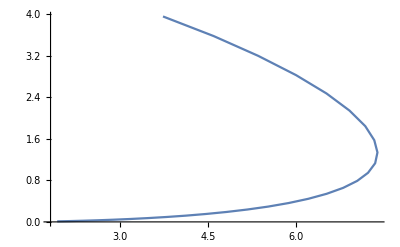

```mathematica
{lVal,dVal}={4,1.05};
δ2FTable4=Table[{ΔVal,δ2aF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal},δ2bF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal}},{ΔVal,6,20,0.5}];
ListPlot[Transpose[{δ2FTable4[[All,2]],δ2FTable4[[All,3]]}],PlotRange->All,Joined->True]
```

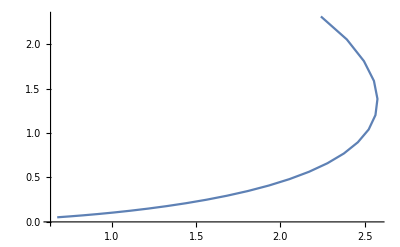

```mathematica
{lVal,dVal}={6,1.05};
δ2FTable6=Table[{ΔVal,δ2aF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal},δ2bF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal}},{ΔVal,8,20,0.5}];
ListPlot[Transpose[{δ2FTable6[[All,2]],δ2FTable6[[All,3]]}],PlotRange->All,Joined->True]
```

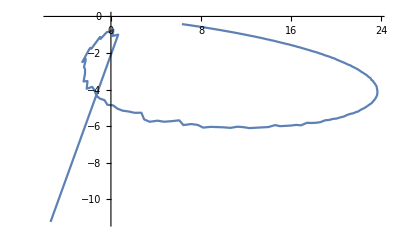

```mathematica
{lVal,dVal}={0,1.05};
δ2FTable0=Table[{ΔVal,δ2aF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal},δ2bF/.{a->0.0001,b->0.0001,l->lVal,Δ->ΔVal,d->dVal}},{ΔVal,1.01,20,0.1}];
ListPlot[Transpose[{δ2FTable0[[All,2]],δ2FTable0[[All,3]]}],PlotRange->All,Joined->True]
```

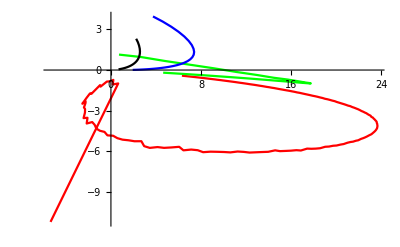

```mathematica
Show[ListPlot[Transpose[{δ2FTable0[[All,2]],δ2FTable0[[All,3]]}],PlotRange->All,Joined->True,PlotStyle->Red],
ListPlot[Transpose[{δ2FTable2[[All,2]],δ2FTable2[[All,3]]}],PlotRange->All,Joined->True,PlotStyle->Green],
ListPlot[Transpose[{δ2FTable4[[All,2]],δ2FTable4[[All,3]]}],PlotRange->All,Joined->True,PlotStyle->Blue],
ListPlot[Transpose[{δ2FTable6[[All,2]],δ2FTable6[[All,3]]}],PlotRange->All,Joined->True,PlotStyle->Black],PlotRange->All]
```

```mathematica
p3
```

p3

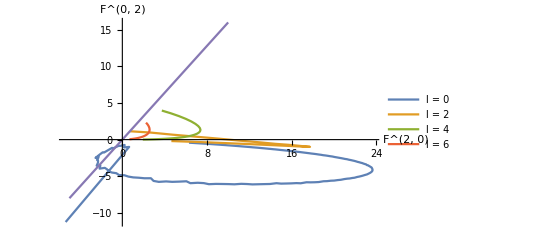

```mathematica
p3={δ2aF/.{a->0.0001,b->0.0001,l->2,Δ->4,d->1.05},δ2bF/.{a->0.0001,b->0.0001,l->2,Δ->4,d->1.05}};
ListPlot[{Transpose[{δ2FTable0[[All,2]],δ2FTable0[[All,3]]}],
Transpose[{δ2FTable2[[All,2]],δ2FTable2[[All,3]]}],
Transpose[{δ2FTable4[[All,2]],δ2FTable4[[All,3]]}],
Transpose[{δ2FTable6[[All,2]],δ2FTable6[[All,3]]}],
Transpose[{Table[x,{x,-5,10}],Table[p3[[2]]/p3[[1]] y,{y,-5,10}]}]},PlotRange->All,Joined->True,PlotLegends->{"l = 0","l = 2","l = 4","l = 6"},AxesLabel->{"F^(2, 0)","F^(0, 2)"}]
```

```mathematica
projectd1p05=ListPlot[{Transpose[{δ2FTable0[[All,2]],δ2FTable0[[All,3]]}],
Transpose[{δ2FTable2[[All,2]],δ2FTable2[[All,3]]}],
Transpose[{δ2FTable4[[All,2]],δ2FTable4[[All,3]]}],
Transpose[{δ2FTable6[[All,2]],δ2FTable6[[All,3]]}],
Transpose[{Table[x,{x,-5,10}],Table[p3[[2]]/p3[[1]] y,{y,-5,10}]}]},PlotRange->All,Joined->True,PlotLegends->{"l = 0","l = 2","l = 4","l = 6"},AxesLabel->{"F^(2, 0)","F^(0, 2)"}]
Export["projectd1p05.jpg",projectd1p05]
```

-Graphics-

projectd1p05.jpg